## Uppgift 1 - Polynomekvation

```mathematica
Hitta lösningarna till polynomekvationen: 2/3 x^5-2/3 x^4-8 x^3+8 x^2+18x-18=0. 
Rita också grafen för polynomet och markera nollställen med en röd punkt.
```

Jag börjar med att definera funktionen f(x)

```mathematica
f[x_]=2/3 x^5-2/3 x^4-8  x^3+8x^2+18x-18
```

-18+18 x+8 x^2-8 x^3-(2 x^4)/3+(2 x^5)/3

Därefter beräknar jag funktionens nollställen, dvs y-värdena då x=0 med funktionen Solve och visualiserar resultatet genom att rita upp funktionens graf med funktionen Plot enligt följande:

```mathematica
{x1,x2,x3,x4,x5}=x/.Solve[f[x]==0]
```

{-3,1,3,-√3,√3}

Polynomekvationen har lösningarna   x1=-3 ⋁ x2=1 ∨ x3=3 ∨ x4=-√3  ⋁  x5=√3

Grafen nedan har dess nollpunkter markerade med röda prickar

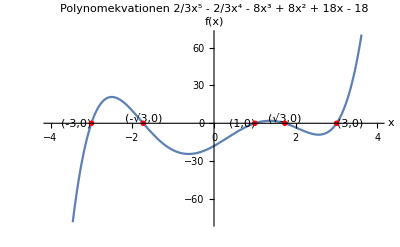

```mathematica
Plot[f[x],{x,-4,4},AxesLabel-> {"x","f(x)"}, PlotLabel -> "Polynomekvationen 2/3x^5 - 2/3x^4 - 8x^3 + 8x^2 + 18x - 18", Epilog -> {Text ["(-3,0)",{x1,f[x1]},Right],Text ["(1,0)",{x2,f[x2]},Right],Text ["(3,0)",{x3,f[x3]},Left],Text ["(-√3,0)",{x4,f[x4]},Bottom],Text ["(√3,0)",{x5,f[x5]},Bottom],
PointSize[0.01],Red,Point[{{x1,f[x1]},{x2,f[x2]},{x3,f[x3]},{x4,f[x4]},{x5,f[x5]}}]}]
```

## Uppgift 2 - Ekvation med absolutbelopp

## Problemformulering

En ekvation med absolut belopp som ser ut enligt följande skall lösas:  |x-1|+|x-3|=4 och Illustrera lösningsområdet grafiskt. För att lösa ekvationen använder jag mig av Funktionen Reduce.

```mathematica
Clear[*.*]
```

```mathematica
f[x_]=Abs[x-1]+Abs[x-3]
```

Abs[-3+x]+Abs[-1+x]

```mathematica
Reduce[f[x]==4,x,Reals]
```

x==0||x==4

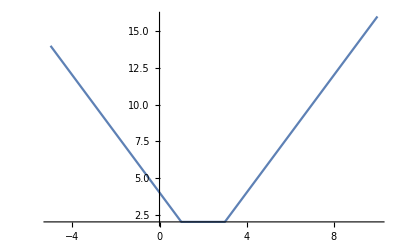

```mathematica
Plot[Abs[-3+x]+Abs[-1+x]]
```

## Uppgift 3 - Binomisk ekvation

## Problemformulering

Finn lösningen till ekvationen z^7=2-i och visa grafiskt att dessa ligger på en cirkel i det komplexa talplanet

```mathematica
z^7=2-I
```

## Uppgift 4 - Akilles och sköldpaddan

### Problemformulering

En paradox är ett påstående som förefaller korrekt utifrån sanna antaganden men leder till självmotsägelser eller till logiskt oacceptabla slutsatser [Wikipedia]. 

Akilles och sköldpaddan är en av Zenons paradoxer. Antag att Akilles springer 10 gånger så fort som sköldpaddan. De båda skall tävla vem som först kommer i mål på 100 meter. Då sköldpaddan är långsammare än Akilles så får den ett försprång på 80 meter. Paradoxen är att när Akilles har sprungit dessa 80 meter, så har sköldpaddan kommit 8 meter, när Akilles har sprungit dessa 8 meter har sköldpaddan kommit 8 dm. Det resonemanget skulle leda till att Akilles aldrig kommer i kapp sköldpaddan. 

Undersök och förklara paradoxen genom att rita tid-sträcka grafer för Akilles och Sköldpaddan. Dessutom beskriv en formel för talföljden ovan och beräkna serien för den med hjälp av Mathematica.

När kommer Akilles i kapp sköldpaddan? 

Visa paradoxen både numeriskt och grafiskt.

```mathematica
Achilles100m={{0,0},{8,80},{8.8,88}};
Sköldpadda100m={{0,80},{8,88},{8.8,88.8}};
```

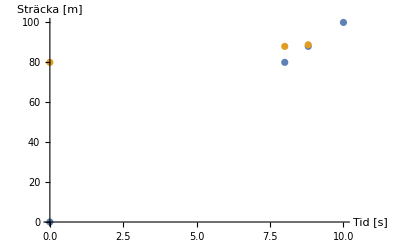

```mathematica
p2=ListPlot[{Achilles100m,Sköldpadda100m},AxesLabel-> {"Tid [s]","Sträcka [m]"}]
```

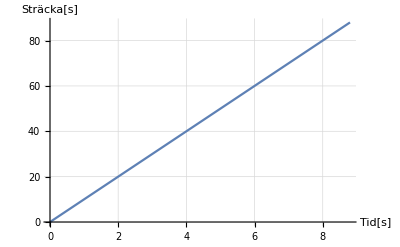

```mathematica
ListLinePlot [Achilles100m,AxesLabel -> {"Tid[s]", "Sträcka[s]"}, PlotStyle->PointSize[ 0.1], GridLines -> Automatic]
```

```mathematica
f[x_]=ax+b
```

ax+b